```mathematica
x=Import["C:\\Users\\hpi\\Desktop\\What Makes a Good Government.csv"];
```

```mathematica
x[[6;;]]//MatrixForm;
```

```mathematica
x=Transpose@DeleteCases[Transpose[x],{_,"","",__}];
```

```mathematica
StringJoin[{"a","s","s"}]
```

ass

```mathematica
labals=StringRiffle[StringExtract[StringReplace[#,{"("->"",")"->"","%"->""}], {1,-2}]]&/@x[[1,3;;]];
```

```mathematica
Length[labals]
```

32

```mathematica
c=Classify[Range[Length[labals]]->labals]
```

ClassifierFunction[…]

```mathematica
cm=ClassifierMeasurements[c,Range[Length[labals]]->labals]
```

ClassifierMeasurementsObject[…]

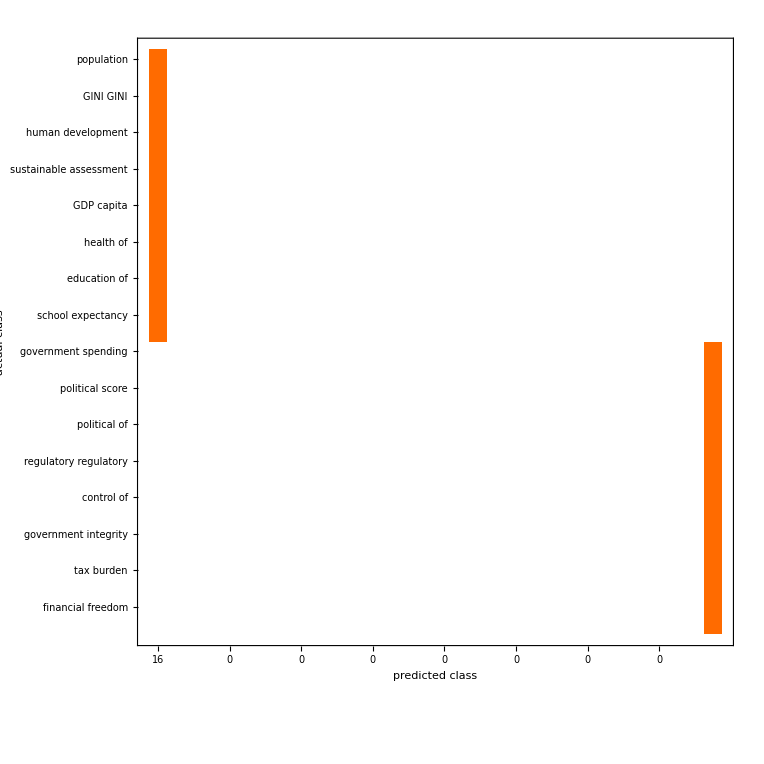

```mathematica
cm["ConfusionMatrixPlot"->labals]
```

```mathematica
labals//MatrixForm
```

(population
surface area
GINI index
happy planet
human development
world happiness
sustainable economic
GDP billions
GDP per
GDP growth
health expenditure
health expenditure
education expenditure
education expenditure
school life
unemployment 
government spending
government expenditure
political rights
civil liberties
political stability
government effectiveness
regulatory quality
rule of
control of
judicial effectiveness
government integrity
property rights
tax burden
overall economic
financial freedom
women MPs)

```mathematica
DeleteCases[x[[6;;200,{1,2}]],{"-",_}]
```

{{Afghanistan,AFG},{Albania,ALB},{Algeria,DZA},{Andorra,AND},{Angola,AGO},{Antigua & Barbuda,ATG},{Argentina,ARG},{Armenia,ARM},{Australia,AUS},{Austria,AUT},{Azerbaijan,AZE},{Bahamas,BHS},{Bahrain,BHR},{Bangladesh,BGD},{Barbados,BRB},{Belarus,BLR},{Belgium,BEL},{Belize,BLZ},{Benin,BEN},{Bhutan,BTN},{Bolivia,BOL},{Bosnia and Herzegovina,BIH},{Botswana,BWA},{Brazil,BRA},{Brunei,BRN},{Bulgaria,BGR},{Burkina Faso,BFA},{Burundi,BDI},{Cabo Verde,CPV},{Cambodia,KHM},{Cameroon,CMR},{Canada,CAN},{Central African Republic,CAF},{Chad,TCD},{Chile,CHL},{China,CHN},{Colombia,COL},{Comoros,COM},{Congo (Dem. Rep.),COD},{Congo (Rep.),COG},{Costa Rica,CRI},{Cote d'Ivoire,CIV},{Croatia,HRV},{Cuba,CUB},{Cyprus,CYP},{Czech Republic,CZE},{Denmark,DNK},{Djibouti,DJI},{Dominica,DMA},{Dominican Republic,DOM},{Ecuador,ECU},{Egypt,EGY},{El Salvador,SLV},{Equatorial Guinea,GNQ},{Eritrea,ERI},{Estonia,EST},{Eswatini,SWZ},{Ethiopia,ETH},{Fiji,FJI},{Finland,FIN},{France,FRA},{Gabon,GAB},{Gambia, The,GMB},{Georgia,GEO},{Germany,DEU},{Ghana,GHA},{Greece,GRC},{Grenada,GRD},{Guatemala,GTM},{Guinea,GIN},{Guinea-Bissau,GNB},{Guyana,GUY},{Haiti,HTI},{Honduras,HND},{Hungary,HUN},{Iceland,ISL},{India,IND},{Indonesia,IDN},{Iran,IRN},{Iraq,IRQ},{Ireland,IRL},{Israel,ISR},{Italy,ITA},{Jamaica,JAM},{Japan,JPN},{Jordan,JOR},{Kazakhstan,KAZ},{Kenya,KEN},{Kiribati,KIR},{Korea (Dem. People’s Rep.),PRK},{Korea (Rep.),KOR},{Kosovo,-},{Kuwait,KWT},{Kyrgyzstan,KGZ},{Laos,LAO},{Latvia,LVA},{Lebanon,LBN},{Lesotho,LSO},{Liberia,LBR},{Libya,LBY},{Liechtenstein,LIE},{Lithuania,LTU},{Luxembourg,LUX},{Macedonia,MKD},{Madagascar,MDG},{Malawi,MWI},{Malaysia,MYS},{Maldives,MDV},{Mali,MLI},{Malta,MLT},{Marshall Islands,MHL},{Mauritania,MRT},{Mauritius,MUS},{Mexico,MEX},{Micronesia,FSM},{Moldova,MDA},{Monaco,MCO},{Mongolia,MNG},{Montenegro,MNE},{Morocco,MAR},{Mozambique,MOZ},{Myanmar,MMR},{Namibia,NAM},{Nauru,NRU},{Nepal,NPL},{Netherlands,NLD},{New Zealand,NZL},{Nicaragua,NIC},{Niger,NER},{Nigeria,NGA},{Norway,NOR},{Oman,OMN},{Pakistan,PAK},{Palau,PLW},{Panama,PAN},{Papua New Guinea,PNG},{Paraguay,PRY},{Peru,PER},{Philippines,PHL},{Poland,POL},{Portugal,PRT},{Qatar,QAT},{Romania,ROU},{Russia,RUS},{Rwanda,RWA},{Saint Kitts and Nevis,KNA},{Saint Lucia,LCA},{Saint Vincent and the Grenadines,VCT},{Samoa,WSM},{San Marino,SMR},{Sao Tome and Principe,STP},{Saudi Arabia,SAU},{Senegal,SEN},{Serbia,SRB},{Seychelles,SYC},{Sierra Leone,SLE},{Singapore,SGP},{Slovakia,SVK},{Slovenia,SVN},{Solomon Islands,SLB},{Somalia,SOM},{South Africa,ZAF},{South Sudan,SSD},{Spain,ESP},{Sri Lanka,LKA},{Sudan,SDN},{Suriname,SUR},{Sweden,SWE},{Switzerland,CHE},{Syria,SYR},{Taiwan,TWN},{Tajikistan,TJK},{Tanzania,TZA},{Thailand,THA},{Timor-Leste,TLS},{Togo,TGO},{Tonga,TON},{Trinidad and Tobago,TTO},{Tunisia,TUN},{Turkey,TUR},{Turkmenistan,TKM},{Tuvalu,TUV},{Uganda,UGA},{Ukraine,UKR},{United Arab Emirates,ARE},{United Kingdom,GBR},{United States,USA},{Uruguay,URY},{Uzbekistan,UZB},{Vanuatu,VUT},{Venezuela,VEN},{Vietnam,VNM},{Yemen,YEM},{Zambia,ZMB},{Zimbabwe,ZWE}}

```mathematica
data=Table[Correlation[data[[i]],data[[j]]],{i,1,3},{j,1,3}]//N
```

{{1.,0.964579,-1.},{0.964579,1.,-0.964579},{-1.,-0.964579,1.}}

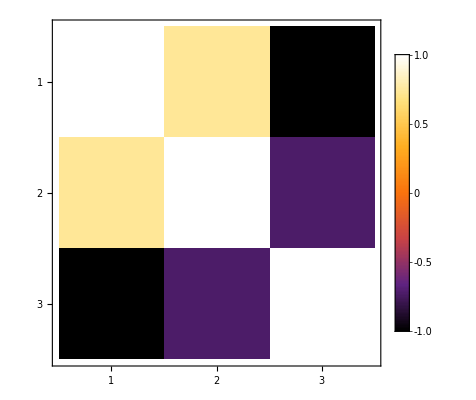

```mathematica
MatrixPlot[data,PlotLegends->Automatic,PlotRange->Automatic,FrameTicks->True,ColorFunction->"SunsetColors"]
```